```mathematica
Quit[]
```

```mathematica
pp/:MakeBoxes[pp,TraditionalForm]:=SuperscriptBox["p","+"]
pm/:MakeBoxes[pm,TraditionalForm]:=SuperscriptBox["p","-"]
xp/:MakeBoxes[xp,TraditionalForm]:=SuperscriptBox["x","+"]
xm/:MakeBoxes[xm,TraditionalForm]:=SuperscriptBox["x","-"]
Xp/:MakeBoxes[Xp,TraditionalForm]:=SuperscriptBox["X","+"]
Xm/:MakeBoxes[Xm,TraditionalForm]:=SuperscriptBox["X","-"]
Zp/:MakeBoxes[Zp,TraditionalForm]:=SuperscriptBox["Z","+"]
Zm/:MakeBoxes[Zm,TraditionalForm]:=SuperscriptBox["Z","-"]
pT/:MakeBoxes[pT,TraditionalForm]:=ToBoxes[p̲]
pT2/:MakeBoxes[pT2,TraditionalForm]:=SuperscriptBox["p̲","2"]
ScalarProduct/:MakeBoxes[ScalarProduct[p_],TraditionalForm]:=SuperscriptBox["p","2"]
```

```mathematica
p̲//FullForm
```

UnderBar[p]

```mathematica
δp={pp-(kp-kpp)/2,pm-(pT2/(2 kp)-pT2/(2 kpp))/2}
```

{1/2 (-kp+kpp)+pp,pm+1/2 (-pT2/(2 kp)+pT2/(2 kpp))}

```mathematica
solki=FullSimplify[Solve[δp==0,{kp,kpp}]]
```

{{kp→pp-(√(pm pp (2 pm pp-pT2)))/(√2 pm),kpp→-pp-(√(pm pp (2 pm pp-pT2)))/(√2 pm)},{kp→pp+(√(pm pp (2 pm pp-pT2)))/(√2 pm),kpp→-pp+(√(pm pp (2 pm pp-pT2)))/(√2 pm)}}

```mathematica
solki={{kp->pp-(√(pm pp (2 pm pp-pT2)))/(√2 pm),kpp->-pp-(√(pm pp (2 pm pp-pT2)))/(√2 pm)},{kp->pp+(√(pm pp (2 pm pp-pT2)))/(√2 pm),kpp->-pp+(√(pm pp (2 pm pp-pT2)))/(√2 pm)}};
```

```mathematica
solkm=FullSimplify[{pT2/(2 kp),pT2/(2 kpp)}/.solki]
```

{{pm+(√(pm pp (2 pm pp-pT2)))/(√2 pp),-pm+(√(pm pp (2 pm pp-pT2)))/(√2 pp)},{pm-(√(pm pp (2 pm pp-pT2)))/(√2 pp),-pm-(√(pm pp (2 pm pp-pT2)))/(√2 pp)}}

```mathematica
ki={kp,kpp};
```

```mathematica
Jp=Table[D[δp[[i]],ki[[j]]],{i,1,2},{j,1,2}]
```

{{-1/2,1/2},{pT2/(4 kp^2),-pT2/(4 kpp^2)}}

```mathematica
FullSimplify[kp kpp/.solki]
FullSimplify[Det[Jp]/.solki]
d=FullSimplify[kp kpp Det[Jp]/.solki]
```

{-(pp pT2)/(2 pm),-(pp pT2)/(2 pm)}

{-(√2 pm √(pm pp (2 pm pp-pT2)))/(pp pT2),(√2 pm √(pm pp (2 pm pp-pT2)))/(pp pT2)}

{(√(pm pp (2 pm pp-pT2)))/(√2),-(√(pm pp (2 pm pp-pT2)))/(√2)}

```mathematica
d={(√(pm pp (2 pm pp-pT2)))/(√2),-(√(pm pp (2 pm pp-pT2)))/(√2)};
```

Note that we should take d[[2]] as the correct result because we need to take the absolute value of Jp.

```mathematica
Proj:=Exp[-I (kp+kpp) xm -I (pT2/(2 kp)+pT2/(2 kpp)) xp]{{-pT2/(kp kpp),pT/kp},{-pT/kpp,1}}/d[[2]]
```

```mathematica
free=FullSimplify[Exp[-I (kp+kpp) xm -I (pT2/(2 kp)+pT2/(2 kpp)) xp]/4/d[[2]]]
```

-ⅇ^(-(ⅈ (kp+kpp) (2 kp kpp xm+pT2 xp))/(2 kp kpp))/(2 √2 √(pm pp (2 pm pp-pT2)))

```mathematica
FullSimplify[(free/.solki[[1]])+(free/.solki[[2]])]
```

-(cos((√(4 pm pp-2 pT2) (pm xp-pp xm))/(√pm √pp)))/(√2 √(pm pp (2 pm pp-pT2)))

```mathematica
g22=FullSimplify[(Proj/.solki[[1]])+(Proj/.solki[[2]])]
```

{{-(4 √2 pm Cos[(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)])/(pp √(pm pp (2 pm pp-pT2))),-(4 pT (√2 pm pp Cos[(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)]+ⅈ √pm √pp √(2 pm pp-pT2) Sin[(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)]))/(pp √(pm pp (2 pm pp-pT2)) pT2)},{(-4 √2 pm pp pT Cos[(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)]+4 ⅈ √pm √pp pT √(2 pm pp-pT2) Sin[(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)])/(pp √(pm pp (2 pm pp-pT2)) pT2),-(2 √2 Cos[(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)])/(√(pm pp (2 pm pp-pT2)))}}

```mathematica
g22={{-(4 √2 pm Cos[(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)])/(pp √(pm pp (2 pm pp-pT2))),-(4 pT (√2 pm pp Cos[(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)]+ⅈ √pm √pp √(2 pm pp-pT2) Sin[(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)]))/(pp √(pm pp (2 pm pp-pT2)) pT2)},{(-4 √2 pm pp pT Cos[(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)]+4 ⅈ √pm √pp pT √(2 pm pp-pT2) Sin[(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)])/(pp √(pm pp (2 pm pp-pT2)) pT2),-(2 √2 Cos[(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)])/(√(pm pp (2 pm pp-pT2)))}};
```

```mathematica
FullSimplify[(2 √2 Cos[(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)])/(√(pm pp (2 pm pp-pT2)))/.{(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)->c √(2 pm pp-pT2)}/.{2 pm pp-pT2->ScalarProduct[p],4 pm pp-2pT2->2 ScalarProduct[p]}//TraditionalForm]
```

(2 √2 cos(c √(p^2)))/(√(p^- p^+ p^2))

```mathematica
mat=FullSimplify[Expand[g22]/((2 √2 Cos[(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)])/(√(pm pp (2 pm pp-pT2))))/.{(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)->c √(2 pm pp-pT2)}/.{2 pm pp-pT2->ScalarProduct[p],4 pm pp-2pT2->2 ScalarProduct[p]}]
```

{{-(2 pm)/pp,-(2 pm pT+(ⅈ √2 √pm pT √ScalarProduct[p] Tan[c √ScalarProduct[p]])/(√pp))/pT2},{(-2 pm pT+(ⅈ √2 √pm pT √ScalarProduct[p] Tan[c √ScalarProduct[p]])/(√pp))/pT2,-1}}

```mathematica
FullSimplify[-mat//TraditionalForm]
```

((2 p^-)/p^+ | (2 p^- p̲+(ⅈ √2 √(p^-) √(p^2) tan(c √(p^2)) p̲)/(√(p^+)))/(p̲)^2
(2 p^- p̲-(ⅈ √2 √(p^-) p̲ √(p^2) tan(c √(p^2)))/(√(p^+)))/(p̲)^2 | 1)

```mathematica
FullSimplify[mat[[1,2]]-mat[[2,1]]]
```

-(2 ⅈ √2 √pm pT √ScalarProduct[p] Tan[c √ScalarProduct[p]])/(√pp pT2)

```mathematica
(√(4 pm pp-2 pT2) (pp xm-pm xp))/(√pm √pp)//TraditionalForm
```

(√(4 p^- p^+-2 (p̲)^2) (p^+ x^--p^- x^+))/(√(p^-) √(p^+))

```mathematica
Clear[η]
```

```mathematica
Solve[{τ==Sqrt[2 xp xm],η==1/2 Log[xp/xm]},{xp,xm}]
```

{{xp→-(ⅇ^η τ)/(√2),xm→-(ⅇ^-η τ)/(√2)},{xp→(ⅇ^η τ)/(√2),xm→(ⅇ^-η τ)/(√2)}}

```mathematica
τη={Sqrt[2 xp xm],1/2 Log[xp/xm]};
xpm={xp,xm};
```

```mathematica
Jτη=Table[D[τη[[i]],xpm[[j]]],{i,1,2},{j,1,2}]
```

(xm/(√2 √(xm xp)) | xp/(√2 √(xm xp))
1/(2 xp) | -1/(2 xm))

```mathematica
Det[Jτη]
```

-(√(xm xp))/(√2 xm xp)

```mathematica
FullSimplify[Integrate[1/(Sqrt[τ^2+τY^2- τ τY Exp[η-y]]^3),τY]/.{τY->0},τ>0]
```

(2 ⅇ^(η+y))/(τ^2 (ⅇ^(2 η)-4 ⅇ^(2 y)))

```mathematica
FullSimplify[FullSimplify[Integrate[1/(zp (xm-(xp-zp) Exp[-2 y]) Sqrt[2] Exp[y]),zp]/.{zp->xp}]/.{xp->1/Sqrt[2] τ Exp[η],xm->1/Sqrt[2] τ Exp[-η]},τ>0&&η>0&&y>0]
FullSimplify[FullSimplify[Integrate[1/(zp (xm-(xp-zp) Exp[-2 y]) Sqrt[2] Exp[y]),zp]]/.{xp->1/Sqrt[2] τ Exp[η],xm->1/Sqrt[2] τ Exp[-η]},τ>0&&η>0&&y>0]
```

((η-y) csch(y-η))/τ

(csch(y-η) (log(zp)-log(√2 τ ⅇ^y sinh(y-η)+zp)))/(2 τ)

```mathematica
1/Csch[x]
```

sinh(x)

```mathematica
δpm={2pp pm - pT2,η-1/2 Log[pp/pm]}
p={pp,pm}
```

{2 pm pp-pT2,η-1/2 log(pp/pm)}

{pp,pm}

```mathematica
solppm=FullSimplify[Solve[δpm==0,p],η>0]
```

{{pp→-(ⅇ^η √pT2)/(√2),pm→-(ⅇ^-η √pT2)/(√2)},{pp→(ⅇ^η √pT2)/(√2),pm→(ⅇ^-η √pT2)/(√2)}}

```mathematica
Jpm=Table[D[δpm[[i]],p[[j]]],{i,1,2},{j,1,2}]
```

(2 pm | 2 pp
-1/(2 pp) | 1/(2 pm))

```mathematica
Det[Jpm]/.solppm
```

{2,2}

#### Z^+, Z^- integrations

```mathematica
Zpm={Zp,Zm};
δZ={1/2 Log[(Xp-Zp)/(Xm-Zm)]-1/2 Log[pp/pm],pm+p1T^2/(2((p2T+p3T) (Zp/(2Zm))^(1/2)-pp))-(p2T+p3T)(Zm/(2Zp))^(1/2)}
```

{1/2 log((Xp-Zp)/(Xm-Zm))-1/2 log(pp/pm),p1T^2/(2 (((p2T+p3T) √(Zp/Zm))/(√2)-pp))-((p2T+p3T) √(Zm/Zp))/(√2)+pm}

```mathematica
FullForm["∈"]
```

"\[Element]"

```mathematica
FullSimplify[FullSimplify[Expand[2((p2T+p3T) (Zp/(2Zm))^(1/2)-pp) (pm+p1T^2/(2((p2T+p3T) (Zp/(2Zm))^(1/2)-pp))-(p2T+p3T)(Zm/(2Zp))^(1/2))],Zp>0&&Zm>0]/.{Zp-> 1/Sqrt[2] τ Exp[η],Zm-> 1/Sqrt[2] τ Exp[-η],pp-> 1/Sqrt[2] pT Exp[y],pm-> 1/Sqrt[2] pT Exp[-y]},η∈Reals]
```

p1T^2+2 pT (p2T+p3T) cosh(y-η)-(p2T+p3T)^2-pT^2

```mathematica
JZ=Table[D[δZ[[i]],Zpm[[j]]],{i,1,2},{j,1,2}]
```

(-1/(2 (Xp-Zp)) | 1/(2 (Xm-Zm))
((p2T+p3T) Zm)/(2 √2 √(Zm/Zp) Zp^2)-(p1T^2 (p2T+p3T))/(4 √2 Zm √(Zp/Zm) (((p2T+p3T) √(Zp/Zm))/(√2)-pp)^2) | (p1T^2 (p2T+p3T) Zp)/(4 √2 Zm^2 √(Zp/Zm) (((p2T+p3T) √(Zp/Zm))/(√2)-pp)^2)-(p2T+p3T)/(2 √2 √(Zm/Zp) Zp))

```mathematica
FullSimplify[Det[JZ],Zp>0&&Zm>0]
```

-((p2T+p3T) (Xp Zm-Xm Zp) (-√2 p1T^2 √(Zm Zp)+√2 p2T^2 √(Zm Zp)-4 pp Zm (p2T+p3T)+2 √2 p2T p3T √(Zm Zp)+√2 p3T^2 √(Zm Zp)+2 √2 pp^2 Zm √(Zm/Zp)))/(4 Zm^2 Zp (Zm-Xm) (Zp-Xp) (√2 (p2T+p3T) √(Zp/Zm)-2 pp)^2)

```mathematica
d=FullSimplify[2 Zp Zm Sqrt[2 (Xp-Zp) (Xm-Zm)]Det[JZ],Zp>0&&Zm>0]
```

((p2T+p3T) (Xm Zp-Xp Zm) (-√2 p1T^2 √(Zm Zp)+√2 p2T^2 √(Zm Zp)-4 pp Zm (p2T+p3T)+2 √2 p2T p3T √(Zm Zp)+√2 p3T^2 √(Zm Zp)+2 √2 pp^2 Zm √(Zm/Zp)))/(√2 Zm √((Xm-Zm) (Xp-Zp)) (√2 (p2T+p3T) √(Zp/Zm)-2 pp)^2)

```mathematica
d=((p2T+p3T) (Xm Zp-Xp Zm) (-√2 p1T^2 √(Zm Zp)+√2 p2T^2 √(Zm Zp)-4 pp Zm (p2T+p3T)+2 √2 p2T p3T √(Zm Zp)+√2 p3T^2 √(Zm Zp)+2 √2 pp^2 Zm √(Zm/Zp)))/(√2 Zm √((Xm-Zm) (Xp-Zp)) (√2 (p2T+p3T) √(Zp/Zm)-2 pp)^2)
```

((p2T+p3T) (Xm Zp-Xp Zm) (-√2 p1T^2 √(Zm Zp)+√2 p2T^2 √(Zm Zp)-4 pp Zm (p2T+p3T)+2 √2 p2T p3T √(Zm Zp)+√2 p3T^2 √(Zm Zp)+2 √2 pp^2 Zm √(Zm/Zp)))/(√2 Zm √((Xm-Zm) (Xp-Zp)) (√2 (p2T+p3T) √(Zp/Zm)-2 pp)^2)

```mathematica
Series[1/d/.{Xp->τ/Sqrt[2],Xm->τ/Sqrt[2],Zp->zp τ,Zm->zm τ},{τ,Infinity,1}]
```

(√2 zm √(zm zp-zm/(√2)-zp/(√2)+1/2) (√2 (p2T+p3T) √(zp/zm)-2 pp)^2)/(τ (p2T+p3T) (zp/(√2)-zm/(√2)) (-√2 p1T^2 √(zm zp)+√2 p2T^2 √(zm zp)+2 √2 p2T p3T √(zm zp)-4 p2T pp zm+√2 p3T^2 √(zm zp)-4 p3T pp zm+2 √2 pp^2 zm √(zm/zp)))+O((1/τ)^2)

```mathematica
+
```

```mathematica
solZpm=FullSimplify[Solve[{(1-Zp)/(1-Zm)==pp/pm,pm+p1T^2/(2(c (Zp/Zm)^(1/2)-pp))==c (Zm/Zp)^(1/2)},{Zp,Zm}],c>0&&pp>0&&pm>0&&(c (Zp/Zm)^(1/2)-pp)>0]
```

$Aborted

```mathematica
Solve[{pm+p1T2/(2(c x-pp))==c/x},x]/.{c->1/Sqrt[2] (p2T+p3T),x->(Zp/Zm)^(1/2)}
```

{{√(Zp/Zm)→(-√((p1T2-(p2T+p3T)^2-2 pm pp)^2-8 pm pp (p2T+p3T)^2)-p1T2+(p2T+p3T)^2+2 pm pp)/(2 √2 pm (p2T+p3T))},{√(Zp/Zm)→(√((p1T2-(p2T+p3T)^2-2 pm pp)^2-8 pm pp (p2T+p3T)^2)-p1T2+(p2T+p3T)^2+2 pm pp)/(2 √2 pm (p2T+p3T))}}

```mathematica
d={((2 c^2+2 pm pp-pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) (pp Xm-pm Xp) (-4 √((c^2 (pp Xm-pm Xp)^2)/(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) c^2+(2 (-4 c^4+2 (4 pm pp+2 pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) c^2+(2 pm pp-pT2) (-2 pm pp+pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2))) (pm Xp-pp Xm) c)/(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)-1/(2 √2 (4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2))pp √(-(-4 c^4+2 (2 pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) c^2+(2 pm pp-pT2) (-2 pm pp+pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))/(c^2 pp^2)) (4 c^4-2 (4 pm pp+2 pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) c^2-(2 pm pp-pT2) (-2 pm pp+pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2))) (pp Xm-pm Xp)+2 pT1 √((c^2 (pp Xm-pm Xp)^2)/(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2))) (4 (pp Xm+pm Xp) c^4+2 (pp √(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xm-pm √(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xp-2 (2 pm pp+pT2) (pp Xm+pm Xp)) c^2+(2 pm pp-pT2) (2 pp Xp pm^2+(2 pp^2 Xm-(pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) Xp) pm+pp (√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)-pT2) Xm)))/(√2 c pm^2 pp √(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) (c √((8 c^4+4 (√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)-2 pT2) c^2+2 (2 pm pp-pT2) (2 pm pp-pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))/(c^2 pm^2))-4 pp)^2 (pm Xp-pp Xm) √(1/(pm pp (4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)^2)(4 (pp Xm+pm Xp) c^4-2 (2 pp (2 pm pp+pT2) Xm-pp √(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xm+2 pm (2 pm pp+pT2) Xp+pm √(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xp) c^2+(2 pm pp-pT2) (2 pp Xp pm^2+(2 pp^2 Xm-(pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) Xp) pm+pp (√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)-pT2) Xm))^2)),((2 c^2+2 pm pp-pT2-√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) (-4 √((c^2 (pp Xm-pm Xp)^2)/(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) c^2+(2 (4 c^4+2 (-4 pm pp-2 pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) c^2+(2 pm pp-pT2) (2 pm pp-pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2))) (pp Xm-pm Xp) c)/(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)-1/(2 √2 (4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2))pp √((4 c^4+2 (√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)-2 pT2) c^2+(2 pm pp-pT2) (2 pm pp-pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))/(c^2 pp^2)) (4 c^4+2 (-4 pm pp-2 pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) c^2+(2 pm pp-pT2) (2 pm pp-pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2))) (pp Xm-pm Xp)+2 pT1 √((c^2 (pp Xm-pm Xp)^2)/(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2))) (4 (pp Xm+pm Xp) c^4+2 (-pp √(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xm+pm √(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xp-2 (2 pm pp+pT2) (pp Xm+pm Xp)) c^2+(2 pm pp-pT2) (2 pp Xp pm^2+(2 Xm pp^2-pT2 Xp+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xp) pm-pp (pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) Xm)))/(16 √2 c pm^2 pp √(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) (pp-(c √(-(-4 c^4+2 (2 pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) c^2+(2 pm pp-pT2) (-2 pm pp+pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))/(c^2 pm^2)))/(2 √2))^2 √(1/(pm pp (4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)^2)(4 (pp Xm+pm Xp) c^4+2 (-2 pp (2 pm pp+pT2) Xm-pp √(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xm-2 pm (2 pm pp+pT2) Xp+pm √(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xp) c^2+(2 pm pp-pT2) (2 pp Xp pm^2+(2 Xm pp^2-pT2 Xp+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xp) pm-pp (pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) Xm))^2)),(c (pp Xm-pm Xp) (-4 √((c^2 (pp Xm-pm Xp)^2)/((2 c^2-2 pm pp+pT2)^2)) c^2-(2 (2 c^2-2 pm pp+pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) (pm Xp-pp Xm) c)/(2 c^2-2 pm pp+pT2)-(pp (2 c^2-2 pm pp+pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) √((pm (2 c^2-2 pm pp+pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))/(pp (-2 c^2+2 pm pp-pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))) (pm Xp-pp Xm))/(-2 c^2+2 pm pp-pT2)+2 pT1 √((c^2 (pp Xm-pm Xp)^2)/((2 c^2-2 pm pp+pT2)^2))) (-2 (pp Xm+pm Xp) c^2+pp (√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)-pT2) Xm+2 pm^2 pp Xp+pm (2 pp^2 Xm-(pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) Xp)))/(√2 pm (2 c^2-2 pm pp+pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) (pp-c √((pp (-2 c^2+2 pm pp-pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))/(pm (2 c^2-2 pm pp+pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))))^2 (pm Xp-pp Xm) √(((pp (2 c^2-2 pm pp+pT2) Xm-pp √(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xm+pm (2 c^2-2 pm pp+pT2) Xp+pm √(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xp)^2)/(pm pp (2 c^2-2 pm pp+pT2)^2))),(c (-4 √((c^2 (pp Xm-pm Xp)^2)/((2 c^2-2 pm pp+pT2)^2)) c^2-(2 (2 c^2-2 pm pp+pT2-√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) (pm Xp-pp Xm) c)/(2 c^2-2 pm pp+pT2)-(pp (-2 c^2+2 pm pp-pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) √((pm (-2 c^2+2 pm pp-pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))/(pp (2 c^2-2 pm pp+pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))) (pp Xm-pm Xp))/(-2 c^2+2 pm pp-pT2)+2 pT1 √((c^2 (pp Xm-pm Xp)^2)/((2 c^2-2 pm pp+pT2)^2))) (-2 (pp Xm+pm Xp) c^2-pp (pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) Xm+2 pm^2 pp Xp+pm (2 Xm pp^2-pT2 Xp+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xp)))/(√2 pm (-2 c^2+2 pm pp-pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) (pp-c √((pp (2 c^2-2 pm pp+pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))/(pm (-2 c^2+2 pm pp-pT2+√(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))))^2 √(((pp (2 c^2-2 pm pp+pT2) Xm+pp √(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xm+pm (2 c^2-2 pm pp+pT2) Xp-pm √(4 c^4+4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) Xp)^2)/(pm pp (2 c^2-2 pm pp+pT2)^2)))};
```

```mathematica
FullSimplify[Series[1/d[[1]]/.{Xp->τ/Sqrt[2],Xm->τ/Sqrt[2]},{τ,Infinity,1}]]
```

-((4 (√2 c pm (pm-pp) (c √((8 c^4+4 (√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)-2 pT2) c^2+2 (2 pm pp-pT2) (2 pm pp-pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))/(c^2 pm^2))-4 pp)^2 (4 (pm+pp) c^4+2 (-√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) pm-2 (pm+pp) (2 pm pp+pT2)+pp √(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) c^2+(2 pm pp-pT2) (2 pp pm^2-(-2 pp^2+pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) pm+pp (√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)-pT2)))))/(((pp-pm) (4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)^(3/2) (2 c^2+2 pm pp-pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) √((4 (pm+pp) c^4+2 (-√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2) pm-2 (pm+pp) (2 pm pp+pT2)+pp √(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) c^2+(2 pm pp-pT2) (2 pp pm^2-(-2 pp^2+pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) pm+pp (√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)-pT2)))^2/(pm pp (4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)^2)) (8 √2 √((c^2 (pm-pp)^2)/(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) c^2+(4 √2 (pm-pp) (4 c^4-2 (4 pm pp+2 pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) c^2-(2 pm pp-pT2) (-2 pm pp+pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2))) c)/(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)+1/(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)pp (pp-pm) √(-(-4 c^4+2 (2 pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) c^2+(2 pm pp-pT2) (-2 pm pp+pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))/(c^2 pp^2)) (4 c^4-2 (4 pm pp+2 pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)) c^2-(2 pm pp-pT2) (-2 pm pp+pT2+√(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))-4 √2 pT1 √((c^2 (pm-pp)^2)/(4 c^4-4 (2 pm pp+pT2) c^2+(pT2-2 pm pp)^2)))) τ))+O((1/τ)^2)

```mathematica
Series[1/2 Log[(1-x/τ)/(1-y/τ)],{τ,Infinity,1}]
```

(y-x)/(2 τ)+O((1/τ)^2)

```mathematica
Solve[{zp/zm==c^2,(Xp-zp)/(Xm-zm)==pp/pm},{zp,zm}]
```

{{zp→-(c^2 pp Xm-c^2 pm Xp)/(c^2 pm-pp),zm→-(pp Xm-pm Xp)/(c^2 pm-pp)}}

```mathematica
FullSimplify[ArcCosh[Cosh[x]]]
```

cosh^-1(cosh(x))

```mathematica
FullSimplify[Exp[ArcCosh[x]]]
```

ⅇ^(cosh^-1(x))

```mathematica
Solve[{Zp/Zm==pp/pm Exp[2 Δ],(Xp-Zp)/(Xm-Zm)==pp/pm},{Zp,Zm}]
```

{{Z^+→(ⅇ^(2 Δ) (p^- X^+-p^+ X^-))/((ⅇ^(2 Δ)-1) p^-),Z^-→-(p^+ X^--p^- X^+)/((ⅇ^(2 Δ)-1) p^+)}}

```mathematica
Solve[{Zp/Zm==pp/pm Exp[2 Δ],(Xp-Zp)/(Xm-Zm)==pp/pm},{Zp,Zm}]//StandardForm
```

{{Zp→(ⅇ^(2 Δ) (-pp Xm+pm Xp))/((-1+ⅇ^(2 Δ)) pm),Zm→-(pp Xm-pm Xp)/((-1+ⅇ^(2 Δ)) pp)}}

```mathematica
Zpm[Xp_,Xm_,pp_,pm_,pT_,p2T_,p3T_]:=Module[{Δ,Δn,Δd,p1T,p1Tabs,p2Tabs,p3Tabs,pTabs},
p1T=p2T+p3T-pT;p1Tabs=Sqrt[p1T.p1T];p2Tabs=Sqrt[p2T.p2T];p3Tabs=Sqrt[p3T.p3T];pTabs=Sqrt[pT.pT];
Δn=(p2Tabs+p3Tabs)^2+pTabs^2-p1Tabs^2;Δd=2 pTabs (p2Tabs+p3Tabs);
If[Δn≥Δd,
Δ=ArcCosh[Δn/Δd];
{(ⅇ^(2 Δ) (-pp Xm+pm Xp))/((-1+ⅇ^(2 Δ)) pm),-(pp Xm-pm Xp)/((-1+ⅇ^(2 Δ)) pp)},
Print["No solution!"]]
]
```

```mathematica
Zpm[2,2,1,2,{1,0},{1,-1},{0,1.}]
```

{1.20711,0.414214}

```mathematica
ArcCosh[0.5]
```

0.+1.0472 ⅈ

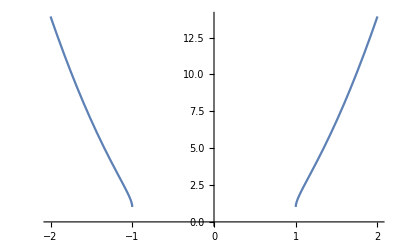

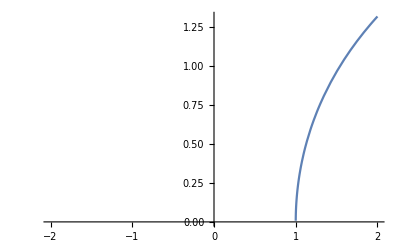

```mathematica
Plot[Exp[2ArcCosh[x]],{x,-2,2}]
Plot[ArcCosh[x],{x,-2,2}]
```

```mathematica
DSolve[D[f[t,p],t]-p/t D[f[t,p],p]==c[t,p],f[t,p],{t,p}]
```

{{f(t,p)→∫_1^t c(K[1],(p t)/K[1])ⅆK[1]+c_1(p t)}}

```mathematica
Quit[]
```

```mathematica
Exit[]
```

```mathematica
δpm={pp+1/Sqrt[2] p1T-p2p-p3p,pT^2/(2 pp)+1/Sqrt[2] p1T-p2T^2/(2 p2p)-p3T^2/(2 p3p)};
p23p={p2p,p3p};
```

```mathematica
solpp=FullSimplify[Solve[δpm==0,p23p]]
```

{{p2p→(√((2 p1T^2 pp+√2 p1T (2 pp^2+pT^2)+2 pp (p2T^2-p3T^2+pT^2))^2-8 p2T^2 pp (√2 p1T+2 pp) (√2 p1T pp+pT^2))+2 p1T^2 pp+√2 p1T (2 pp^2+pT^2)+2 pp (p2T^2-p3T^2+pT^2))/(4 (√2 p1T pp+pT^2)),p3p→(-√((2 p1T^2 pp+√2 p1T (2 pp^2+pT^2)+2 pp (p2T^2-p3T^2+pT^2))^2-8 p2T^2 pp (√2 p1T+2 pp) (√2 p1T pp+pT^2))+2 p1T^2 pp+√2 p1T (2 pp^2+pT^2)+2 pp (-p2T^2+p3T^2+pT^2))/(4 (√2 p1T pp+pT^2))},{p2p→(-√((2 p1T^2 pp+√2 p1T (2 pp^2+pT^2)+2 pp (p2T^2-p3T^2+pT^2))^2-8 p2T^2 pp (√2 p1T+2 pp) (√2 p1T pp+pT^2))+2 p1T^2 pp+√2 p1T (2 pp^2+pT^2)+2 pp (p2T^2-p3T^2+pT^2))/(4 (√2 p1T pp+pT^2)),p3p→(√((2 p1T^2 pp+√2 p1T (2 pp^2+pT^2)+2 pp (p2T^2-p3T^2+pT^2))^2-8 p2T^2 pp (√2 p1T+2 pp) (√2 p1T pp+pT^2))+2 p1T^2 pp+√2 p1T (2 pp^2+pT^2)+2 pp (-p2T^2+p3T^2+pT^2))/(4 (√2 p1T pp+pT^2))}}

```mathematica
Jpm=Table[D[δpm[[i]],p23p[[j]]],{i,1,2},{j,1,2}]
```

(-1 | -1
p2T^2/(2 p2p^2) | p3T^2/(2 p3p^2))

```mathematica
FullSimplify[2 p2p 2 p3p Det[Jpm]/.solpp]
```

{-(√((2 p1T^2 pp+√2 p1T (2 pp^2+pT^2)+2 pp (p2T^2-p3T^2+pT^2))^2-8 p2T^2 pp (√2 p1T+2 pp) (√2 p1T pp+pT^2)))/pp,(√((2 p1T^2 pp+√2 p1T (2 pp^2+pT^2)+2 pp (p2T^2-p3T^2+pT^2))^2-8 p2T^2 pp (√2 p1T+2 pp) (√2 p1T pp+pT^2)))/pp}

```mathematica
DSolve[ϵ'[t]==-ϵ[t]/t-αs^2/t^2,ϵ[t],t]
```

{{ϵ(t)→c_1/t-(αs^2 log(t))/t}}